Adaptation from example problem from Speigel’s Schaum’s series: Theory and Problems of Classical Mechanics

A vertical spring has stiffness factor 16.  If forced with a forcing function of 30 Cos[6 t], plot the position in time.

This is an undamped oscillator with a forcing function.  Not only is the equation for position solved as a differential equation, its position is tracked in time.  In addition to this, I turn “ON” damping at a certain time (for t>5π) and track its effect through the use of a recurrence plot.

```mathematica
Needs["HierarchicalClustering`"]
SetOptions[Plot,ImageSize->Medium,PlotStyle->{Black,Thick},BaseStyle->{FontFamily->"SansSerif",Bold}];
SetOptions[MatrixPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold}];
```

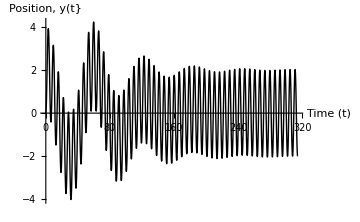
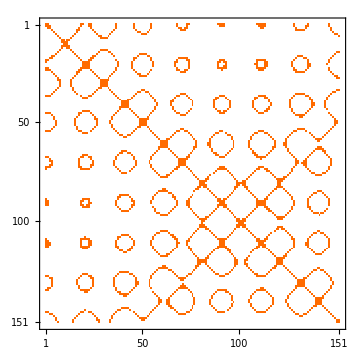
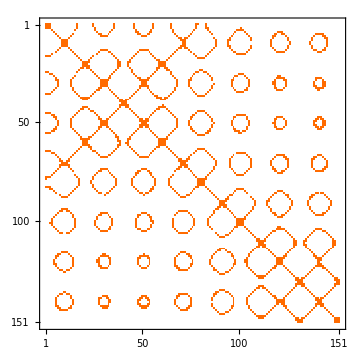
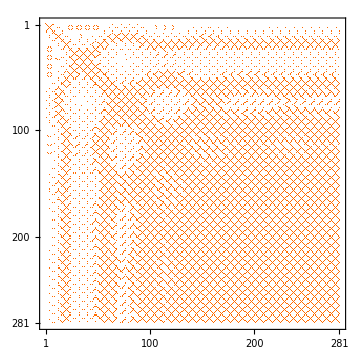

```mathematica
Module[{δ,y,t,s,tmax=100π},
s=NDSolveValue[{15y''[t]+δ[t] y'[t]+.16y[t]==30Cos[t],y[0]==0,y'[0]==0,δ[0]== 0.,WhenEvent[t>15π,δ[t]->.6]},y,{t,0,tmax},DiscreteVariables->δ];
Plot[s[t],{t,0,tmax},AxesLabel->{"Time (t)","Position, y(t}"}]

With[{stepSize=tmax/400,end=tmax},
MatrixPlot[UnitStep[0.1-DistanceMatrix[s[Range[0,15π,tmax/1000]]]]]
MatrixPlot[UnitStep[0.1-DistanceMatrix[s[Range[15π,30π,tmax/1000]]]]]
MatrixPlot[UnitStep[0.1-DistanceMatrix[s[Range[30π,tmax,stepSize]]]]]
]
]
```

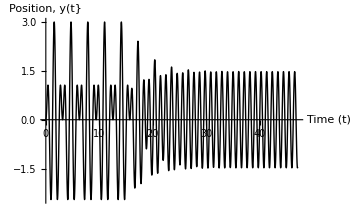

```mathematica
tmax=15π;
s=NDSolveValue[{y''[t]+δ[t] y'[t]+16y[t]==30Cos[6t],y[0]==0,y'[0]==0,δ[0]== 0.,WhenEvent[t>5π,δ[t]->.6]},y,{t,0,tmax},DiscreteVariables->δ];
Plot[s[t],{t,0,tmax},AxesLabel->{"Time (t)","Position, y(t}"}]
```

-Graphics-

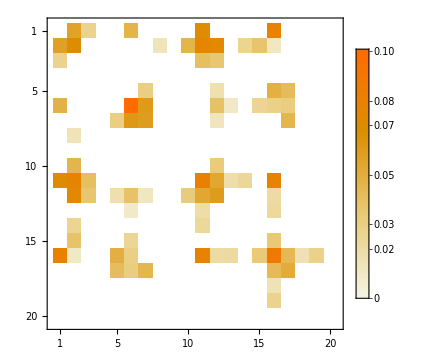

```mathematica
Plot[s[t],{t,0,tmax},AxesLabel->{"Time (t)","Position, y(t}"}]
FData1=Abs[Fourier[UnitStep[0.1-DistanceMatrix[s[Range[0,tmax,tmax/50]]]]]];
FData1[[1,1]]=0;
norm1=Norm[FData1,"Frobenius"];
FData2=FData1/norm1;
thresh1=0.1 Max[FData2];
FData=Threshold[FData2,{"Hard",thresh1}];
FData//Dimensions;

MatrixPlot[FData[[1;;20,1;;20]],BaseStyle->{FontWeight->"Plain",FontSize->25},PlotLegends->Automatic]
```